# Prediction Opportunity MJO

BX Pan
2017.10.26

## Prediction Opportunity

On the Long Term Prediction of Chaotic System

Climate system undergoes different scenarios through its evolution. The slowly varying components can provide information for extended forecast. When dynamical models are initialized at certain phase of these  phenomena, the model forecasts match observations with more fidelity than the neutral phases. These intervals are named as forecast windows and believed to bring prediction opportunities.

## Examples

MJO

```mathematica
mjo=ImageCrop[-Graphics-];
ImageResize[mjo,1000]
```

-Graphics-

-Graphics- | -Graphics-"Meet the MJO, By Jon Gottschalck, NOAA Climate Prediction Center with Andrea Ray, WWA

Methodology

Cluster prediction results according to climate conditions and compare with long-run/neutral conditions.

The method applied here is a little bit different from ENSO.

For ENSO, it is generally easier to quantify/parameterize (even though there are different ENSO types, see this.

For MJO, the quantification/parameterization remains a problem given its organization and seasonality(Weickmann and Berry 2009, Dias et al. 2013, Waliser et al. 2012, Kikuchi et al. 2012, Lee et al.
2013, DeMott et al. 2013). 
The evolution of phase is important.

## MJO Indexes

Parameterization of MJO

1, filter OLR to retain only frequencies associated with the MJO. 
2, Filtered OLR between 208S and 208N is then subjected to a standard covariance matrix EOF analysis that retains the local variance of the OLR fluctuations.

```mathematica
MJO=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/MJO/OMI","Table"];
```

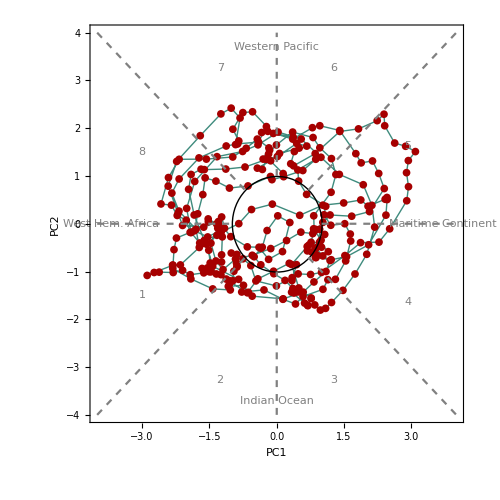

```mathematica
Show[{ListLinePlot[RMM[[1;;300]],
	Frame->True,
	AspectRatio->1,
	ImageSize->Large,
	BaseStyle->25,
	Axes->None,
	FrameLabel->{"PC1","PC2"},
	PlotRange->{{-4.,4.},{-4.,4.}},
	GridLines->None,
	PlotStyle -> Directive[Thick, RGBColor[.8, 0, 0]], 
	ColorFunction ->"BlueGreenYellow" ],
	ListPlot[RMM[[1;;300]]],
	(*ListPlot[RMM[[1;;40]]->Range[10],LabelingFunction->Above],*)

	Graphics[Circle[{0,0},1],AspectRatio->1],
	Plot[0,{x,-4,-1},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[0,{x,1,4},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	ListLinePlot[{{0,-4},{0,-1}},PlotStyle->{Gray,Dashed}],
	ListLinePlot[{{0,1},{0,4}},PlotStyle->{Gray,Dashed}],
	Plot[x,{x,-4,-Sqrt[2]/2},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[x,{x,Sqrt[2]/2,4},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[-x,{x,-4,-Sqrt[2]/2},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Plot[-x,{x,Sqrt[2]/2,4},AspectRatio->1,PlotStyle->{Gray,Dashed}],
	Graphics[Style[Text["1", {-3, -1.5}, {0,0}],Gray]],
	Graphics[Style[Text["2", {-1.26, -3.27}, {0,0}],Gray]],
	Graphics[Style[Text["3", {1.26, -3.27}, {0,0}],Gray]],
	Graphics[Style[Text["4", {2.92, -1.63}, {0,0}],Gray]],
	Graphics[Style[Text["5", {2.92, 1.63}, {0,0}],Gray]],
	Graphics[Style[Text["6", {1.26, 3.27}, {0,0}],Gray]],
	Graphics[Style[Text["7", {-1.26, 3.27}, {0,0}],Gray]],
	Graphics[Style[Text["8", {-3, 1.5}, {0,0}],Gray]],
	Graphics[Style[Text["Western Pacific", {0, 3.7}, {0,0}],Gray]],
	Graphics[Style[Text["Indian Ocean", {0, -3.7}, {0,0}],Gray]],
	Graphics[Rotate[Style[Text["West Hem. Africa", {-3.7, 0}, {0,0}],Gray],Pi/2]],
	Graphics[Rotate[Style[Text["Maritime Continent", {3.7,0}, {0,0}],Gray],3Pi/2]]
	},
	Frame->True,
	ImageSize->500,
	FrameLabel->{"PC1","PC2"}]
```

```mathematica
Dimensions[RMM]
```

{14177,2}

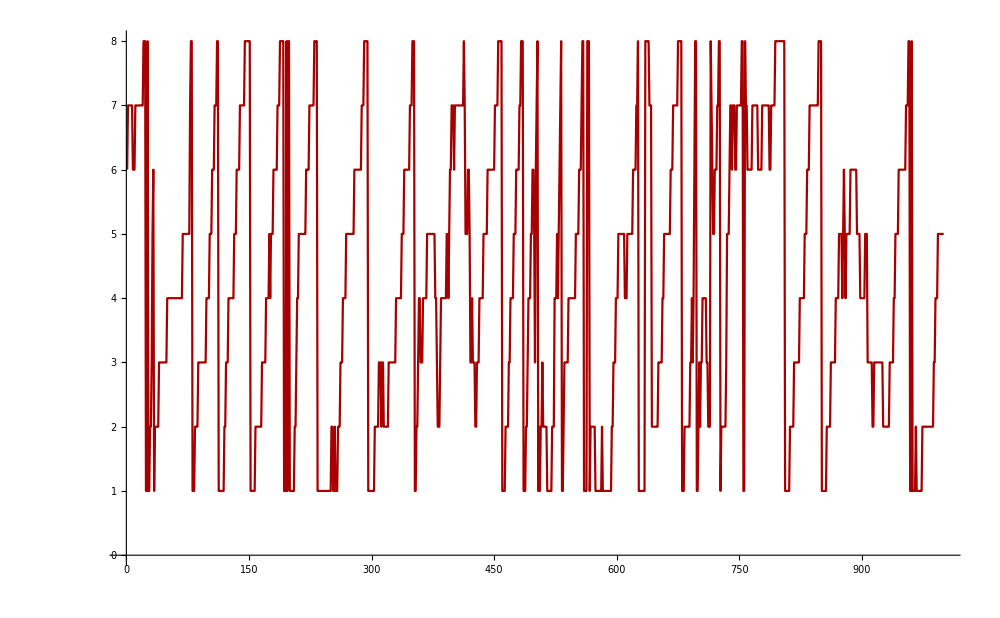

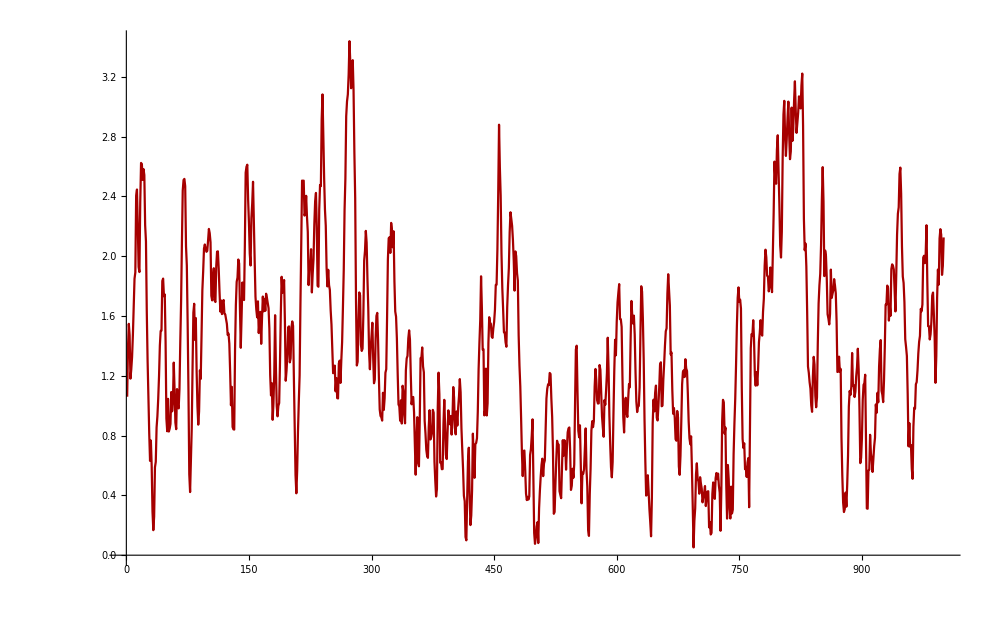

```mathematica
ListLinePlot[phase[[1;;1000]],ImageSize->1000]
ListLinePlot[Map[Sqrt[(#[[1]]^2+#[[2]]^2)]&,RMM][[1;;1000]],ImageSize->1000]
```

```mathematica
T=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/MJO/RMM.nc",{"Datasets","T"}][[1676;;]];
RMM1=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/MJO/RMM.nc",{"Datasets","RMM1"}][[1676;;]];
RMM2=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/MJO/RMM.nc",{"Datasets","RMM2"}][[1676;;]];
phase=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/ClimateIndex/MJO/RMM.nc",{"Datasets","phase"}][[1676;;]];
RMM=Transpose[{RMM1,RMM2}];
intensity=Map[Sqrt[(#[[1]]^2+#[[2]]^2)]&,RMM];
```

```mathematica
Dimensions[phase]
```

{14177}

```mathematica
Dimensions[intensity]
```

{14177}